# Quantum Particle in a Box

A little paradox, traced to a failure of hermiticity

Nicholas Wheeler
10 January 2010
Revised 16 January, in response to some observations by David Griffiths, Darrell Schroeder & Joel Franklin

### Introduction

A quantum particle of mass m moves on the interval 0 < x < a. The Hamiltonian opearator is standardly taken to have the form

H=-ℏ^2/(2m)∂_(x,x) □

As a matter of computational (mainly graphic) convenience I set a = 1. The normalized energy-eigenstates are

```mathematica
e[x_,n_]:=√2 Sin[n π x]
Table[∫_0^1 e[x,m]e[x,n]ⅆx,{m,1,4},{n,1,4}]//TableForm
```

1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1

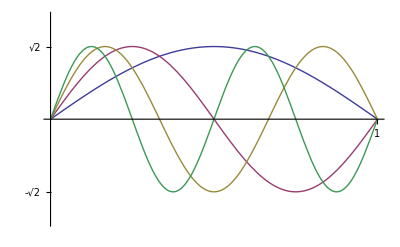

```mathematica
Plot[{e[x,1],e[x,2], e[x,3],e[x,4]},{x,0,1}, Ticks->{{1},{-√2,√2}}, PlotRange->{-2,2}]
```

From

```mathematica
ℰ=(π^2 ℏ^2)/(2 m);
```

```mathematica
-ℏ^2/(2m)D[e[x,1],{x,2}]==ℰ e[x,1]
-ℏ^2/(2m)D[e[x,2],{x,2}]==2^2 ℰ e[x,2]
-ℏ^2/(2m)D[e[x,3],{x,2}]==3^2 ℰ e[x,3]
-ℏ^2/(2m)D[e[x,4],{x,2}]==4^2 ℰ e[x,4]
```

True

True

True

«1 more identical outputs»

we see that the n^th energy eigenvalue is given by

ℰ_n=ℰ n^2

The paradoxical results that are the point of this discussion emerge when we assume the (momentary initial) state of the system to have the simple form of the following…

### Parabolic test state

We declare an interest in the polynomial state

```mathematica
ψ[x_]:=√30 x(1-x)
```

which is seen to be normalized:

```mathematica
∫_0^1 ψ[x]^2 ⅆx
```

1

I use a graphic technique to compare the parabolic state to the ground state:

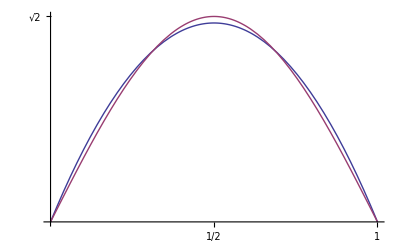

```mathematica
Plot[{ψ[x],e[x,1]},{x,0,1}, Ticks->{{1/2,1},{√2}}, GridLines->{{0.5},{√(15/8),√2}}]
```

In constructing the figure I have taken note of the fact that ψ[x] is maximal at x = 1/2, where it assumes the value

```mathematica
ψ[1/2]==√(15/8)
```

True

The figure establishes that the ground state is by itself a good approximation to ψ. 

Fourier analysis enables us to improve upon the approximation:

```mathematica
Table[{n,∫_0^1 ψ[x]e[x,n]ⅆx},{n,1,13}]//Simplify//TableForm
```

1 | (8 √15)/π^3
2 | 0
3 | (8 √(5/3))/(9 π^3)
4 | 0
5 | (8 √(3/5))/(25 π^3)
6 | 0
7 | (8 √15)/(343 π^3)
8 | 0
9 | (8 √(5/3))/(243 π^3)
10 | 0
11 | (8 √15)/(1331 π^3)
12 | 0
13 | (8 √15)/(2197 π^3)

That—as these results display—only the odd eigenstates contribute to the development of ψ is made obvious by an elementary symmetry argument. A very simple formula serves to describe the Fourier coefficients of odd order:

```mathematica
Table[{n,∫_0^1 ψ[x]e[x,n]ⅆx-(8 √15)/(π^3 n^3)},{n,1,13,2}]//Simplify//TableForm
```

1 | 0
3 | 0
5 | 0
7 | 0
9 | 0
11 | 0
13 | 0

We are led thus to define expansion coefficients

```mathematica
c[k_]:=1/(2k+1)^3(8 √15)/π^3
```

which are found to satisfy the normalization condition

```mathematica
∑_(k=0)^∞ c[k]^2
```

1

and manage to do so in excellent approximation even when the series is severely truncated:

```mathematica
Table[{n,N[∑_(k=0)^n c[k]^2,12]},{n,0,10}]//TableForm
```

0 | 0.998555014364
1 | 0.999924774329
2 | 0.99998868185
3 | 0.999997169427
4 | 0.999999048385
5 | 0.999999612043
6 | 0.99999981892
7 | 0.999999906585
8 | 0.999999947954
9 | 0.999999969179
10 | 0.999999980822

With their aid, we construct

```mathematica
∑_(k=0)^∞ c[k]e[x,2k+1]
```

-1/π^3 ⅈ √(15/2) ⅇ^(-ⅈ π x) (-LerchPhi[ⅇ^(-2 ⅈ π x),3,1/2]+ⅇ^(2 ⅈ π x) LerchPhi[ⅇ^(2 ⅈ π x),3,1/2])

That function does not look to be real-valued, and certainly does not look at all like the simple polynomial √30 x(1-x), but seems on the following graphic evidence to check out:

```mathematica
SpectralΨ[x_]:=-1/π^3 ⅈ √(15/2) ⅇ^(-ⅈ π x) (-LerchPhi[ⅇ^(-2 ⅈ π x),3,1/2]+ⅇ^(2 ⅈ π x) LerchPhi[ⅇ^(2 ⅈ π x),3,1/2])
```

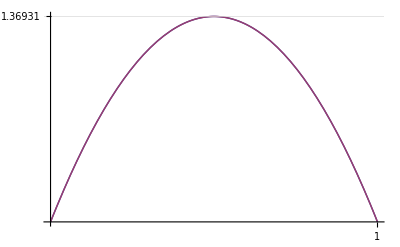

```mathematica
Plot[{ψ[x],SpectralΨ[x]},{x,0,1},Ticks->{{1},{N[√(15/8)]}}, GridLines->{{},{N[√(15/8)]}}]
```

The preceding Fourier series provides already quite a good-looking approximation even when one abandons all but the first few terms:

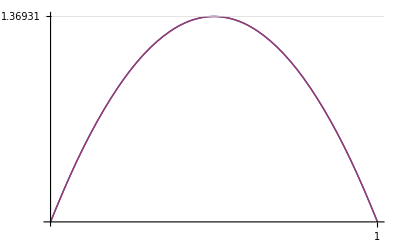

```mathematica
Plot[{ψ[x],∑_(k=0)^5 c[k]e[x,2k+1]},{x,0,1},Ticks->{{1},{N[√(15/8)]}}, GridLines->{{},{N[√(15/8)]}}]
```

How good? Look to the difference:

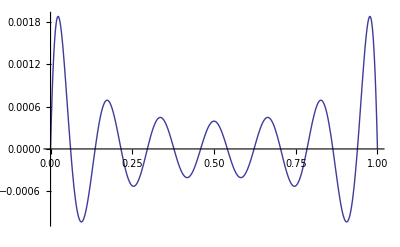

```mathematica
Plot[{ψ[x]-∑_(k=0)^5 c[k]e[x,2k+1]},{x,0,1}]
```

Note the occurance of Gibbs phenomenon, which becomes progressively more marked (relatively, not absolutely) as the order of the approximation increases:

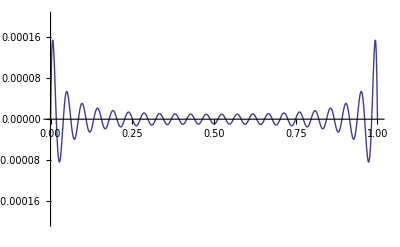

```mathematica
Plot[{ψ[x]-∑_(k=0)^20 c[k]e[x,2k+1]},{x,0,1}, PlotRange->{-.0002,.0002}]
```

### Expected value of energy

Let the Hamiltonian

H=-ℏ^2/(2m)∂_(x,x) □

be abbreviated

-ℋ∂_(x,x) □

where evidently

```mathematica
ℋ=ℏ^2/(2m);
```

From

```mathematica
(-ℋ D[e[x,n], x,x])/e[x,n]
```

(n^2 π^2 ℏ^2)/(2 m)

we recover the information that the n^th eigenvalue can be written ℰ n^2 with

```mathematica
ℰ== π^2 ℋ
```

True

Working directly from

ψ[x,a]==√30 x (1-x)

True

we get

```mathematica
ExpectedEnergy=∫_0^1 ψ[x](-ℋ D[ψ[x],{x,2}])ⅆx
```

(5 ℏ^2)/m

If, on the other hand, we display ψ as a weighted superposition of energy eigenfunctions (i.e., if we work from the spectral representation of ψ) we get

```mathematica
SpectrallyExpectedEnergy=ℰ∑_(k=0)^∞ c[k]^2(2k+1)^2
```

(5 ℏ^2)/m

These results are in perfect agreement:

```mathematica
ExpectedEnergy==SpectrallyExpectedEnergy
```

True

Had we worked with truncated spectral representations of ψ we would have obtained nearly correct results:

```mathematica
Table[{n,ℰ N[∑_(k=0)^n c[k]^2(2k+1)^2,10]},{n,5,50,5}]//TableForm
```

5 | (4.99953117 ℏ^2)/m
10 | (4.999923187 ℏ^2)/m
15 | (4.999974985 ℏ^2)/m
20 | (4.999988927 ℏ^2)/m
25 | (4.999994163 ℏ^2)/m
30 | (4.999996556 ℏ^2)/m
35 | (4.9999978 ℏ^2)/m
40 | (4.999998511 ℏ^2)/m
45 | (4.999998946 ℏ^2)/m
50 | (4.999999226 ℏ^2)/m

in which connection we note that the convergence appears to be logarithmically (?) slow.

### DIGRESSION: Comparison of direct and spectral derivative structures

```mathematica
Dψ=D[ψ[x],x];
DDψ=D[ψ[x],{x,2}];
DDDψ=D[ψ[x],{x,3}];
```

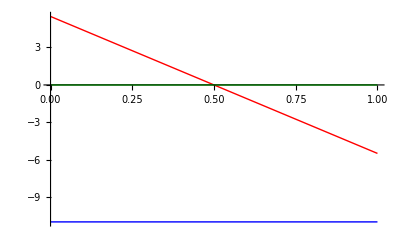

```mathematica
Plot[{Dψ,DDψ,DDDψ},{x,0,1}, PlotStyle->{{Red,Thick},{Blue,Thick},{Green,Thick}}]
```

```mathematica
DSpectralΨ=D[SpectralΨ[x],x];
DDSpectralΨ=D[SpectralΨ[x],{x,2}];
DDDSpectralΨ=D[SpectralΨ[x],{x,3}];
```

The spectral descriptions of those quite-simple functions are quite complicated, so Mathematica takes a minute or two to construct he following figure:

```mathematica
Fig1=Plot[Evaluate[DSpectralΨ],{x,0,1}, PlotStyle->{Red,Thick}];
Fig2=Plot[Evaluate[DDSpectralΨ],{x,0,1}, PlotStyle->{Blue,Thick}];
Fig3=Plot[Evaluate[DDDSpectralΨ],{x,0,1}, PlotStyle->{Green,Thick}];
```

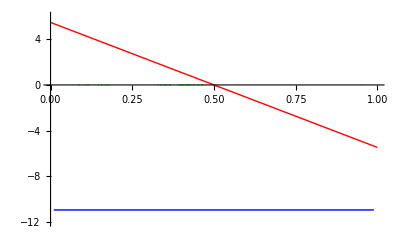

```mathematica
Show[Fig1, Fig2, Fig3,PlotRange->{-12,6}]
```

And the simplest of the functions was evidently posed for Mathematica the greatest computational challenge (notice how the green curve is broken). 

Mathematica has less difficulty if one works in finite approximation; i.e., with truncated series:

```mathematica
Ψ[x_]:=∑_(k=0)^10 c[k]e[x,2k+1]
DΨ=D[Ψ[x],x];
DDΨ=D[Ψ[x],{x,2}];
DDDΨ=D[Ψ[x],{x,3}];
```

```mathematica
fig1=Plot[Evaluate[DΨ],{x,0,1}, PlotStyle->{Red}];
fig2=Plot[Evaluate[DDΨ],{x,0,1}, PlotStyle->{Blue}];
fig3=Plot[Evaluate[DDDΨ],{x,0,1}, PlotStyle->{Green}];
```

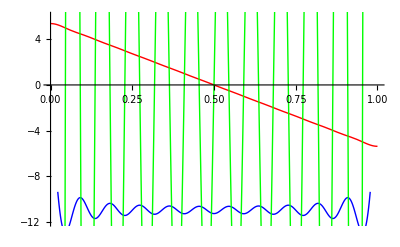

```mathematica
Show[fig1, fig2,fig3,PlotRange->{-12,6}]
```

But, as the figure illustrates, truncation leads to imprecisions that become rapidly more conspicuous as the order of the differentiation increases. I increase the number of terms in the truncated series, and look in finer detail to the results:

```mathematica
ΨΨ[x_]:=∑_(k=0)^50 c[k]e[x,2k+1]
DΨΨ=D[ΨΨ[x],x];
DDΨΨ=D[ΨΨ[x],{x,2}];
DDDΨΨ=D[ΨΨ[x],{x,3}];
```

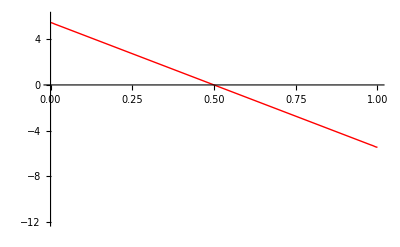

```mathematica
Plot[Evaluate[DΨΨ],{x,0,1}, PlotStyle->{Red}, PlotRange->{-12,6}]
```

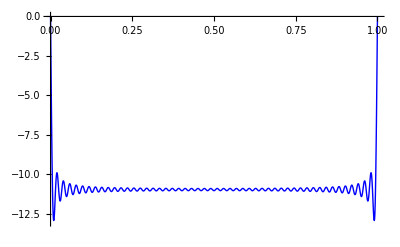

```mathematica
Plot[Evaluate[DDΨΨ],{x,0,1}, PlotStyle->{Blue}, PlotPoints->50, PlotRange->{-13,0}]
```

Gibbs phenomenon is the dominant feature of the preceding figure. It is even more conspicuous in the following figure

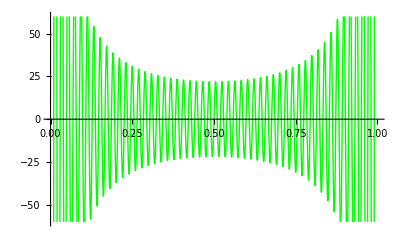

```mathematica
Plot[Evaluate[DDDΨΨ],{x,0,1}, PlotStyle->{Green}, PlotPoints->50, PlotRange->{-60,60}]
```

of which this is a 10× magnification:

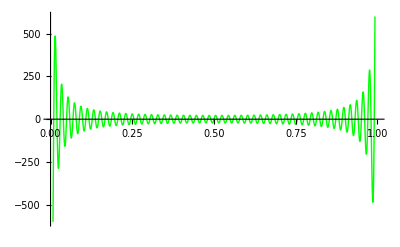

```mathematica
Plot[Evaluate[DDDΨΨ],{x,0,1}, PlotStyle->{Green}, PlotPoints->50, PlotRange->{-600,600}]
```

If we call that function f(x) then it is only in an approximate (meaning averaged) sense that it is the zero function, though we can expect to have

∫_0^1 (slowly changing funcion)f(x)ⅆx≈0

except possibly for Gibbsian end effects.

The reason one must keep more and more terms to get good approximations to exact results emerges when one compares

```mathematica
(8 √30)/(π^3 n^3)e[x,n];
D[%,x]
D[%,x]
D[%,x]
D[%,x]
D[%,x]
```

(16 √15 Cos[n π x])/(n^2 π^2)

-(16 √15 Sin[n π x])/(n π)

-16 √15 Cos[n π x]

16 √15 n π Sin[n π x]

16 √15 n^2 π^2 Cos[n π x]

The short of it: the n^-3 factors that were responsible for the initially rapid convergence lose force with each differentiation, disappear altogether after 3 differentiations, and thereafter become "divergence factors."

### Expected value of energysquared

```mathematica
ExpectedEnergySquared=∫_0^1 ψ[x](ℋ^2 D[ψ[x],{x,4}])ⅆx
```

0

That result is surprising, but understandable: ψ[x] is a quadratic function of x, so is killed by 4th order differentiation. 

If, on the other hand, we proceed from the spectral representation of ψ we already got

```mathematica
SpectrallyExpectedEnergy=ℰ∑_(k=0)^∞ c[k]^2(2k+1)^2
```

(5 ℏ^2)/m

and now get

```mathematica
SpectrallyExpectedEnergySquared=ℰ^2∑_(k=0)^∞ c[k]^2(2k+1)^4
```

(30 ℏ^4)/m^2

which is non-zero. We have arrived at a contradiction:

```mathematica
ExpectedEnergySquared-SpectrallyExpectedEnergySquared
```

-(30 ℏ^4)/m^2

In third order (as in all higher orders) the results yielded by the two methods differ even more profoundly: the first method yields 0 in every case, while the second method leads in every case to series that (for the reason stated just above) diverge: we have

```mathematica
SpectrallyExpectedEnergyCubed=ℰ^3∑_(k=0)^p c[k]^2(2k+1)^6
```

(120 (1+p) ℏ^6)/m^3

which blows up in the limit p ⟶ ∞.

The evident source of the contradiction: we have arrived at a situation in which

```mathematica
derivative of infinite sum ≠infinite sum of derivatives
```

derivative infinite of sum≠derivatives infinite of sum

REMARK: It is clear already on dimensional grounds that relaxation of our assumption that the box width a = 1 entails

ℏ^2/m→ℏ^2/(m a^2)

### Variance

By definition

Variance=ExpectedEnergySquared-(ExpectedEnergy)^2

The spectral method supplies

```mathematica
SpectrallyExpectedEnergySquared-(SpectrallyExpectedEnergy)^2
```

(5 ℏ^4)/m^2

while direct calculation leads to the nonsensical result

```mathematica
ExpectedEnergySquared-(ExpectedEnergy)^2
```

-(25 ℏ^4)/m^2

### Dynamical manifestation of the same problem

Working as before from

```mathematica
H=-ℋ∂_(x,x) □
```

0

we expect to have

```mathematica
Clear[ℋ]
ϕ[x,t]=∑_(k=0)^∞ 1/(k!)(-ⅈ/ℏ ℋ t)^k D[ϕ[x],{x,2k}]
ℋ=ℏ^2/(2m);
```

∑_(k=0)^∞ ((-(ⅈ t ℋ)/ℏ)^k ϕ^(2 k)[x])/(k!)

Looking to the motion of the individual energy eigenfunctions, we have

```mathematica
Table[{k,D[e[x,n],{x,2k}]/e[x,n]},{k,0,4}]//TableForm
```

0 | 1
1 | -n^2 π^2
2 | n^4 π^4
3 | -n^6 π^6
4 | n^8 π^8

whence

```mathematica
∑_(k=0)^∞ 1/(k!)(-ⅈ/ℏ ℋ t)^k(-n^2 π^2)^k(nth.eigenstate)
```

ⅇ^((ⅈ n^2 π^2 t ℏ)/(2 m)) nth.eigenstate

which—when we recall that

```mathematica
ℰ n^2
```

(n^2 π^2 ℏ^2)/(2 m)

is just ℰ_n—gives back the familiar fact that the energy eigenstates simply buzz:

```mathematica
Subscript[(nth.eigenstate), t]=ⅇ^(ⅈ/ℏ Subscript[ℰ, n] t)Subscript[(nth.eigenstate), 0]
```

ⅇ^((ⅈ t ((π^2 ℏ^2)/(2 m))_n)/ℏ) (nth.eigenstate)_0

Here I automate the demonstration:

```mathematica
Clear[ℋ,ℰ]
∑_(k=0)^∞ 1/(k!)(-ⅈ ℋ t)^k D[e[x,n],{x,2k}]
%/.D[(√2 Sin[n π x]), {x,2 k}]->(-n^2 π^2)^k √2 Sin[n π x];
%/.ⅈ n^2 π^2 t ℋ->ⅈ/ℏ Subscript[ℰ, n] t
ℋ=ℏ^2/(2m);
ℰ=n^2 π^2 ℋ;
```

∑_(k=0)^∞ ((-ⅈ t ℋ)^k ∂_{x,2 k} (√2 Sin[n π x]))/(k!)

√2 ⅇ^((ⅈ t ℰ_n)/ℏ) Sin[n π x]

Given the spectral representation of a state, we have only to launch each of its components into motion to set the whole state into motion. Which we now demonstrate as it pertains to the parabolic test state. Define

```mathematica
e[x_,n_,t_]:=e[x,n] ⅇ^(-ⅈ n^2 t)
```

where as a matter of computational convenience I have set ℰ/ℏ = 1. Construct the truncated spectral series (I want only provide proof of method, though we know that inclusion of higher-order terms would have little quantitative effect)

```mathematica
Ψ[x_,t_]:=∑_(k=0)^2 c[k]e[x,2k+1,t]
```

and use

```mathematica
CompConj[A_] := A /.Complex[0,n_]->-Complex[0,n]
```

to construct

```mathematica
ConjΨ[x_,t_]:=CompConj[Ψ[x,t]]
```

Those functions look like this

```mathematica
Ψ[x,t]
ConjΨ[x,t]
```

(8 √30 ⅇ^(-ⅈ t) Sin[π x])/π^3+(8 √(10/3) ⅇ^(-9 ⅈ t) Sin[3 π x])/(9 π^3)+(8 √(6/5) ⅇ^(-25 ⅈ t) Sin[5 π x])/(25 π^3)

(8 √30 ⅇ^(ⅈ t) Sin[π x])/π^3+(8 √(10/3) ⅇ^(9 ⅈ t) Sin[3 π x])/(9 π^3)+(8 √(6/5) ⅇ^(25 ⅈ t) Sin[5 π x])/(25 π^3)

and become rapidly more unwieldly as one moves to higher order. Construct

```mathematica
MovingProbDensity[x_,t_]:=ComplexExpand[Ψ[x,t]CompConj[Ψ[x,t]]]
```

```mathematica
MovingProbDensity[x,t]
```

(1920 Cos[t]^2 Sin[π x]^2)/π^6+(1920 Sin[t]^2 Sin[π x]^2)/π^6+(1280 Cos[t] Cos[9 t] Sin[π x] Sin[3 π x])/(9 π^6)+(1280 Sin[t] Sin[9 t] Sin[π x] Sin[3 π x])/(9 π^6)+(640 Cos[9 t]^2 Sin[3 π x]^2)/(243 π^6)+(640 Sin[9 t]^2 Sin[3 π x]^2)/(243 π^6)+(768 Cos[t] Cos[25 t] Sin[π x] Sin[5 π x])/(25 π^6)+(768 Sin[t] Sin[25 t] Sin[π x] Sin[5 π x])/(25 π^6)+(256 Cos[9 t] Cos[25 t] Sin[3 π x] Sin[5 π x])/(225 π^6)+(256 Sin[9 t] Sin[25 t] Sin[3 π x] Sin[5 π x])/(225 π^6)+(384 Cos[25 t]^2 Sin[5 π x]^2)/(3125 π^6)+(384 Sin[25 t]^2 Sin[5 π x]^2)/(3125 π^6)

```mathematica
TrigReduce[%]
```

-1/(759375 π^6)64 (-11406979+11390625 Cos[2 π x]+15625 Cos[6 π x]+729 Cos[10 π x]+3375 Cos[16 t-8 π x]+91125 Cos[24 t-6 π x]+421875 Cos[8 t-4 π x]-91125 Cos[24 t-4 π x]-421875 Cos[8 t-2 π x]-3375 Cos[16 t-2 π x]-421875 Cos[8 t+2 π x]-3375 Cos[16 t+2 π x]+421875 Cos[8 t+4 π x]-91125 Cos[24 t+4 π x]+91125 Cos[24 t+6 π x]+3375 Cos[16 t+8 π x])

```mathematica
ReducedMovingProbDensity[x_,t_]:=-1/(759375 π^6)64 (-11406979+11390625 Cos[2 π x]+15625 Cos[6 π x]+729 Cos[10 π x]+3375 Cos[16 t-8 π x]+91125 Cos[24 t-6 π x]+421875 Cos[8 t-4 π x]-91125 Cos[24 t-4 π x]-421875 Cos[8 t-2 π x]-3375 Cos[16 t-2 π x]-421875 Cos[8 t+2 π x]-3375 Cos[16 t+2 π x]+421875 Cos[8 t+4 π x]-91125 Cos[24 t+4 π x]+91125 Cos[24 t+6 π x]+3375 Cos[16 t+8 π x])
```

Note that the first cycle of this periodic function is complete at time t = 2π/8.

I construct now a figure illustrating how the moving density compares with its initial structure

```mathematica
ψ[x]^2
```

30 (1-x)^2 x^2

```mathematica
Manipulate[Plot[{ψ[x]^2,Evaluate[ReducedMovingProbDensity[x,t]]},{x,0,1},PlotRange->{0,2.5}],{t,0,(2π)/8}]
```

We now abandon the spectral representation, and work directly from

```mathematica
ψ[x]
```

√30 (1-x) x

We then find

```mathematica
Clear[ℋ]
∑_(k=0)^∞ 1/(k!)(-ⅈ ℋ t)^k D[ψ[x],{x,2k}]
```

∑_(k=0)^∞ ((-ⅈ t ℋ)^k ∂_{x,2 k} (√30 (1-x) x))/(k!)

which by

```mathematica
Table[D[(√30 (1-x) x), {x,2 k}],{k,0,10}]
```

{√30 (1-x) x,-2 √30,0,0,0,0,0,0,0,0,0}

gives

```mathematica
∑_(k=0)^10 ((-ⅈ t ℋ)^k D[(√30 (1-x) x), {x,2 k}])/(k!)
```

√30 (1-x) x+2 ⅈ √30 t ℋ

So we have

```mathematica
ψ[x_,t_]:=√30 (1-x) x+2 ⅈ √30 t ℋ
Conjψ[x_,t_]:=CompConj[ψ[x,t]]
```

giving

```mathematica
MMovingProbDensity[x_,t_]:=ComplexExpand[ψ[x,t]CompConj[ψ[x,t]]]
```

```mathematica
MMovingProbDensity[x,t]
```

30 x^2-60 x^3+30 x^4+120 t^2 ℋ^2

The motion of ψ[x, t] is clearly not periodic, nor is it even unitary:

```mathematica
∫_0^1 %ⅆx
```

1+120 t^2 ℋ^2

Our Hamiltonian has revcaled itself to be non-Hermitian.

MEMORANDA

I had stewed about this problem for a couple of days when, on January 7th, I brought the problem to the attention of David Griffiths, who promptly responded as follows:

Nick,

Here's my first guess as to your error: H^2 is not a valid operator (or rather, your second wave function is not in the space of functions for which it is well-defined/Hermitian).  Both your wave functions have kinks at each end, which means that the first derivative is discontinuous and the second carries a delta function.  You get away with ignoring this when you calculate <H> for the "accidental" reason reason that it is multiplied by a function that is zero at the ends, so the delta function does not contribute.  But when you go to H^2 you need two more derivatives (hence the second derivative of the delta function).  Integration by parts transfers them over to the other function, which means you now have the product of two deltas.  For some reason that works in the case of the ground state, but not in the case of the the quadratic.

Is this even vaguely relevant to your problem?

David

When (on January 11th—yesterday) I mentioned the problem with Darrell Schroeter he made an essentially similar remark: he suggested that my wave function might better be written

Ψ[x,a]=ψ[x,a]S[x,a]

where S[x, a] has unit value inside the box and vanishes outside the box. Those remarks/suggestions have motivated the preceeding discussion. 

I end with record of some commands that figured in earlier versions of this notebook, which I preserve for whatever they may someday prove to be worth:

```mathematica
CoeffList=Table[∫_0^1 x e[x,n]ⅆx,{n,1,20}]
```

{(√2)/π,-1/(√2 π),(√2)/(3 π),-1/(2 √2 π),(√2)/(5 π),-1/(3 √2 π),(√2)/(7 π),-1/(4 √2 π),(√2)/(9 π),-1/(5 √2 π),(√2)/(11 π),-1/(6 √2 π),(√2)/(13 π),-1/(7 √2 π),(√2)/(15 π),-1/(8 √2 π),(√2)/(17 π),-1/(9 √2 π),(√2)/(19 π),-1/(10 √2 π)}

```mathematica
∑_(k=1)^20 CoeffList⟦k⟧e[x,k]
```

(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)-Sin[6 π x]/(3 π)+(2 Sin[7 π x])/(7 π)-Sin[8 π x]/(4 π)+(2 Sin[9 π x])/(9 π)-Sin[10 π x]/(5 π)+(2 Sin[11 π x])/(11 π)-Sin[12 π x]/(6 π)+(2 Sin[13 π x])/(13 π)-Sin[14 π x]/(7 π)+(2 Sin[15 π x])/(15 π)-Sin[16 π x]/(8 π)+(2 Sin[17 π x])/(17 π)-Sin[18 π x]/(9 π)+(2 Sin[19 π x])/(19 π)-Sin[20 π x]/(10 π)

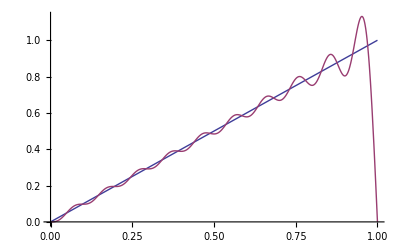

```mathematica
Plot[{x,(2 Sin[π x])/π-Sin[2 π x]/π+(2 Sin[3 π x])/(3 π)-Sin[4 π x]/(2 π)+(2 Sin[5 π x])/(5 π)-Sin[6 π x]/(3 π)+(2 Sin[7 π x])/(7 π)-Sin[8 π x]/(4 π)+(2 Sin[9 π x])/(9 π)-Sin[10 π x]/(5 π)+(2 Sin[11 π x])/(11 π)-Sin[12 π x]/(6 π)+(2 Sin[13 π x])/(13 π)-Sin[14 π x]/(7 π)+(2 Sin[15 π x])/(15 π)-Sin[16 π x]/(8 π)+(2 Sin[17 π x])/(17 π)-Sin[18 π x]/(9 π)+(2 Sin[19 π x])/(19 π)-Sin[20 π x]/(10 π)},{x,0,1}]
```

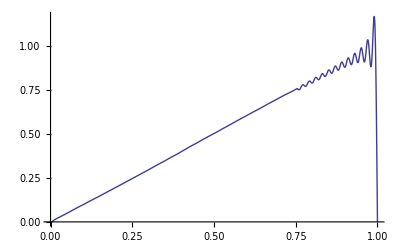

```mathematica
Plot[-∑_(k=1)^100 (-1)^k 2/(k π)Sin[k π x],{x,0,1}]
```

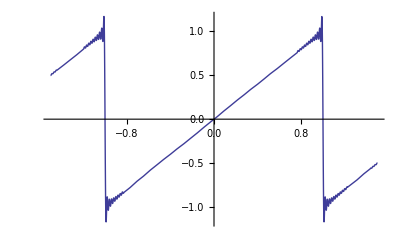

```mathematica
Plot[-∑_(k=1)^100 (-1)^k 2/(k π)Sin[k π x],{x,-1.5,1.5}]
```